```mathematica
nn=551;
Clear[a0,a1,a2,prec]
prec=1001;
```

```mathematica
Α= Table[ If[i==j,a0,If[Mod[i-j,nn]==1,a2,If[Mod[j-i,nn]==1,a1,0]]],{i,1,nn},{j,1,nn}];
γ=1/2//N[#,prec]&;
λ=1/2//N[#,prec]&;
a0=λ//N[#,prec]&;
a1=(1-γ)/2//N[#,prec]&;
a2=(1+γ)/2//N[#,prec]&;
α[θ_]:=(a0+(a2+a1) Cos[θ]);
β[θ_]:=(a1-a2) Sin[θ];
ω[θ_]:=√(α[θ]^2+β[θ]^2);
b[l_]:={{α[(2 π l)/nn],-β[(2 π l)/nn]},{β[(2 π l)/nn],α[(2 π l)/nn]}}
bhat[l_]:=1/ω[(2 π l)/nn] {{α[(2 π l)/nn],-β[(2 π l)/nn]},{β[(2 π l)/nn],α[(2 π l)/nn]}}
B=ConstantArray[0,{nn,nn}];
B⟦1,1⟧=N[α[0],prec];
B⟦nn,nn⟧=N[α[π],prec];
Table[
B⟦2 k;;1+2 k,2 k;;1+2 k⟧=N[b[k],prec];,
{k,1,nn/2-1}];
(*B//MatrixForm;*)
Bhat=ConstantArray[0,{nn,nn}];
Bhat⟦1,1⟧=N[α[0]/ω[0],prec];
Bhat⟦nn,nn⟧=N[ α[π]/ω[π],prec];
Table[
Bhat⟦2 k;;1+2 k,2 k;;1+2 k⟧=N[bhat[k],prec];,
{k,1,nn/2-1}];
OFourier=ConstantArray[0,{nn,nn}];
Table[If[l>1,
OFourier⟦l+1,k+1⟧=N[√(2/nn) Cos[(π l)/nn k],prec],
OFourier⟦1,k+1⟧=N[√(1/nn) Cos[(π l)/nn k],prec]],
{l,0,nn-1,2},{k,0,nn-1}];
Table[
If[l<nn-2,
OFourier⟦l+2,k+1⟧=N[√(2/nn) Sin[(2 π (l/2+1))/nn k],prec],
OFourier⟦nn,k+1⟧=N[√(1/nn) Cos[π k],prec]],
{l,0,nn-1,2},{k,0,nn-1}];
(o1=(Bhat//Transpose).OFourier)//MatrixForm;
(o2=(OFourier//Transpose))//MatrixForm;
MGSDiag= Table[ If[i==j,-1/2,0],{i,1,nn},{j,1,nn}];
(MEsp=Transpose[o1].MGSDiag.Transpose[o2]);

ll=IntegerPart[nn/10];
MEspRed1 = Take[ Take[#,ll]& /@ MEsp, ll];
SVD=SingularValueDecomposition[MEspRed1];
ρ=1/2 ((SVD⟦1⟧)^2+(SVD⟦3⟧)^2);
```

$Aborted

```mathematica
ListPlot3D[ρ,PlotRange->All,ImageSize->Large]
```

-Graphics3D-

Random sampling

```mathematica
nn=80001;
ll=50;
prec=250;
nData=100;
γ=1/2//N[#,prec]&;
λ=1/2//N[#,prec]&;
a0=λ//N[#,prec]&;
a1=(1-γ)/2//N[#,prec]&;
a2=(1+γ)/2//N[#,prec]&;
α[θ_]=(a0+ Cos[θ]);
β[θ_]=(-a1+a2) Sin[θ];
ω[θ_]=Sqrt[α[θ]^2+β[θ]^2];
ϕ[θ_]=ArcTan[α[θ],β[θ]];
t=Table[k,{k,-(nn-1)/2,(nn-1)/2}];
μ=0.0//N[#,prec]&;
βT =0.40824980415756 //N[#,prec]&;
p[l_]:=1/(Exp[βT (ω[((2 π)/nn) l]-μ)]+1);
(*mCos=Table[If[RandomReal[]>p[k],-(1/2)//N[#,prec]&,1/2//N[#,prec]&],{k,1,(nn-1)/2}];
mCos0=If[RandomReal[]>p[0],-(1/2)//N[#,prec]&,1/2//N[#,prec]&];
mSin=Table[If[RandomReal[]>p[k],-(1/2)//N[#,prec]&,1/2//N[#,prec]&],{k,1,(nn-1)/2}];
mSin0=If[RandomReal[]>p[0],-(1/2)//N[#,prec]&,1/2//N[#,prec]&];*)
mCos=Table[-(1/2)//N[#,prec]&,{k,1,(nn-1)/2}];
mCos0=-(1/2)//N[#,prec]&;
mSin=Table[-(1/2)//N[#,prec]&,{k,1,(nn-1)/2}];
mSin0=-(1/2)//N[#,prec]&;

MPlusBand=((If[#==0,(mCos0+mSin0)/2,(mCos⟦Abs[#]⟧+mSin⟦Abs[#]⟧)/2]) E^(I Sign[(2 π)/nn #] ϕ[Abs[(2 π)/nn #]])&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier;
MMinusAntiBand=((If[#==0,(mCos0-mSin0)/2//N[#,prec]&,(mCos⟦Abs[#]⟧-mSin⟦Abs[#]⟧)/2//N[#,prec]&]) E^(I Sign[(2 π)/nn #] (ϕ[Abs[(2 π)/nn #]]))&/@t)//RotateLeft[#,(nn-1)/2]&//Fourier;
```

```mathematica
ll=40;
T=ToeplitzMatrix[Take[MPlusBand,ll],Join[{MPlusBand⟦1⟧},Take[MPlusBand,-ll+1]//Reverse]];
H=HankelMatrix[MMinusAntiBand⟦1;;2*ll-1⟧⟦1;;ll⟧,(MMinusAntiBand⟦1;;2*ll-1⟧//RotateLeft[#,-ll]&)⟦1;;ll⟧];
M=((T+H)/(Sqrt[nn]//N[#,prec]&))//N[#,prec]&;
```

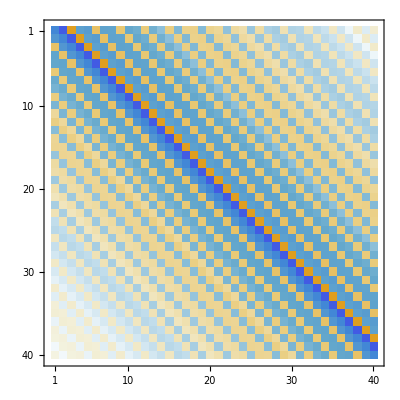

```mathematica
MatrixPlot[M]
```

```mathematica
S=SingularValueDecomposition[M];
P=((S⟦1⟧^2+S⟦3⟧^2)/2 //N[#,prec]&);
```

```mathematica
Export[NotebookDirectory[]<>"Participation_ground.csv",P]
```

/Users/josealejandromontanacortes/Documents/Tesis/XY_model/Participation_ground.csv

```mathematica
ListPlot3D[P,PlotRange->All,ImageSize->Large,ColorFunction->ColorData["RedBlueTones"],FillingStyle->Opacity[0.7],Filling->Automatic,Lighting->Automatic]
```

-Graphics3D-

```mathematica
e
```

Precision 1000

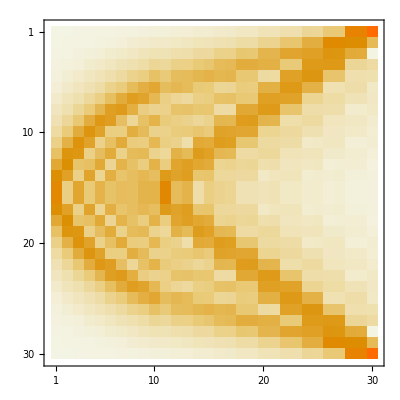

```mathematica
MatrixPlot[P]
```

```mathematica
P2[l_]:=1/(Exp[βT (ω[((2 π)/ll) l]-μ)]+1);
```

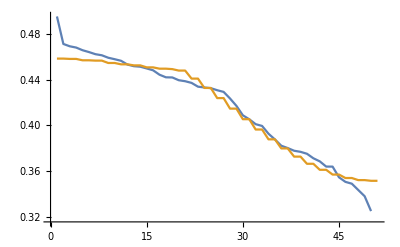

```mathematica
A=ReverseSort[Diagonal[-S⟦2⟧+0.5]];
B=ReverseSort[Table[P2[i],{i,0,ll}]];
ListLinePlot[{A,B},AxesLabel->Automatic]
```

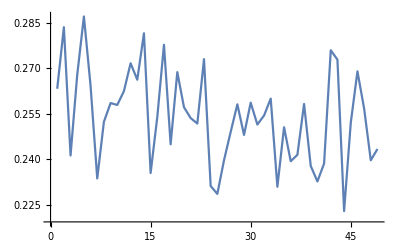

```mathematica
Table[M⟦i+1,i⟧, {i,1,ll-1}]//ListLinePlot
```

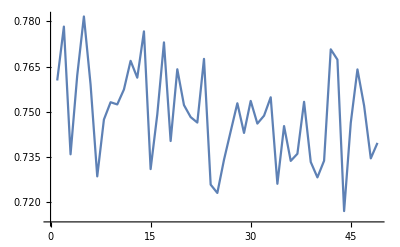

```mathematica
Σ=(-Diagonal[S⟦2⟧]+0.5//N[#,prec]&);
X=Log[1-Σ]-Log[Σ];
M=-((S⟦1⟧.DiagonalMatrix[X].Transpose[S⟦3⟧])/βT);
Table[M⟦i,i+1⟧, {i,1,ll-1}]//ListLinePlot
```

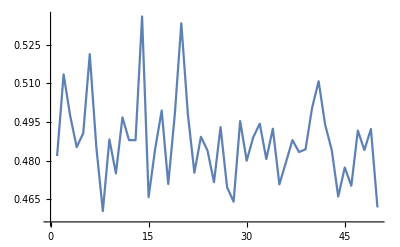

```mathematica
Σ=(-Diagonal[S⟦2⟧]+0.5//N[#,prec]&);
X=Log[1-Σ]-Log[Σ];
M=-((S⟦1⟧.DiagonalMatrix[X].Transpose[S⟦3⟧])/βT);
Table[M⟦i,i⟧, {i,1,ll}]//ListLinePlot
```

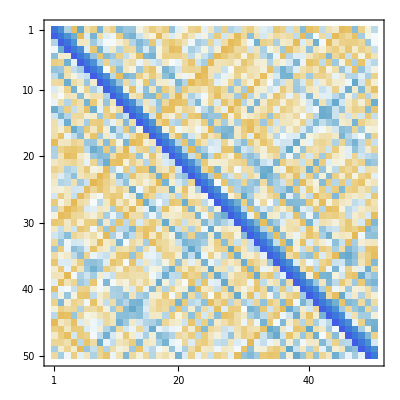

```mathematica
M//MatrixPlot
```

```mathematica
ListPlot3D[M,PlotRange->All,ImageSize->Large]
```

-Graphics3D-

```mathematica
test =Table[i, {i,-10,10}]//RotateLeft[#,10]&;
Take[test,3];
Take[test,-2]
```

```mathematica
a=Join[{test⟦1⟧},Take[test,-2]//Reverse]
```

{0,-1,-2}

```mathematica
T=ToeplitzMatrix[Take[test,3],Join[{test⟦1⟧},Take[test,-2]//Reverse]];
```

```mathematica
T//MatrixForm;
```

```mathematica
use=test⟦1;;2*4-1⟧;
```

```mathematica
(use//RotateLeft[#,-4]&)⟦1;;4⟧;
```

{0,1,2,3}

```mathematica
HankelMatrix[use⟦1;;4⟧,(use//RotateLeft[#,-4]&)⟦1;;4⟧]//MatrixForm
```

(0 | 1 | 2 | 3
1 | 2 | 3 | 4
2 | 3 | 4 | 5
3 | 4 | 5 | 6)